```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

```mathematica
fShowPosterior[n_Integer,xbar_]:=Module[{data,aPosterior1,aPosterior2 },
data = xbar*n;aPosterior1 = BetaDistribution[0.5+ data,n - data + 0.5];
aPosterior2 = BetaDistribution[1+data,n - data + 1];
Plot[{PDF[aPosterior1,x],PDF[aPosterior2,x]},{x,0,1},PlotRange->Full,PlotStyle->{Orange,Blue},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->16},PlotLabel->StringJoin["n = ",ToString@n]]]
```

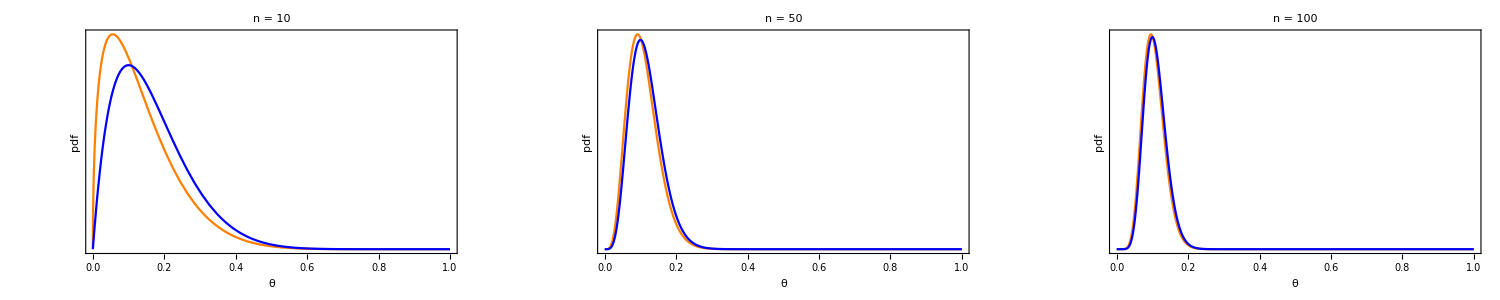

```mathematica
gFinal=Show[GraphicsRow[{fShowPosterior[10,0.1],fShowPosterior[50,0.1],fShowPosterior[100,0.1]}],ImageSize->1500]
```

```mathematica
Export["Objective_jeffreysPrior.pdf",gFinal]
```

Objective_jeffreysPrior.pdf